#### Notebook Description

This notebook is for brain storming.

#### Project Goals

Construct a symbolic representation of a chessboard state (ChessState) and chess moves (ChessMove) in the Wolfram Language.
Develop a function which takes a ChessState and a ChessPlay and returns the new ChessState.
Build a ConvertChessNotation function for converting between the Wolfram and the algebraic chess notation.
Curate a Chess Dataset of famous chess games in the history for the data repository.
Create a ChessStatePlot function which plots a given ChessState on a chessboard. 
Create a ChessMovePlot function that plots the transition from the inputted ChessState to the next state specified by a ChessMove, alongside with a ChessAnimate function that animates a chess game (a dataset or a list of ChessMove’s).
Depending on the amount of remaining time, write a ListGameMove function that receives a ChessState (and ChessRules) and outputs all the possible ChessMove’s. 
Potentially, provide Evaluate → True/”Best” option for ListChessMove which returns sorted and associate predicted winning probabilities/scores for white using an external game engine.
Note: This project will be done keeping in mind that eventually the word Chess in the above functions would be replaced by the word Game, generalizing to as many board and card games possible.

#### Chess Pieces

```mathematica
pieceNamesShort = {"King", "Queen", "Rook", "Bishop", "Knight", "Pawn"};
wpn = Table["White" <> pieceName, {pieceName, pieceNamesShort}];
bpn = Table["Black" <> pieceName, {pieceName, pieceNamesShort}];
pieceNames = wpn ~Join~ bpn;
AppendTo[pieceNames, "EmptySquare"];
```

```mathematica
pieceSymbols = 
	{"♔", "♕", "♖", "♗", "♘", "♙"} ~Join~
	{"♚", "♛", "♜", "♝", "♞", "♟"} ~Join~
	{"□"};
```

```mathematica
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceSymbols;
{♔, ♕, ♖, ♗, ♘, ♙, ♚, ♛, ♜, ♝, ♞, ♟, □} = pieceNames;
```

```mathematica
piecePicLinksWiki =
	{
	"https://upload.wikimedia.org/wikipedia/commons/thumb/4/42/Chess_klt45.svg/75px-Chess_klt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/1/15/Chess_qlt45.svg/75px-Chess_qlt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/7/72/Chess_rlt45.svg/75px-Chess_rlt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/b/b1/Chess_blt45.svg/75px-Chess_blt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/7/70/Chess_nlt45.svg/75px-Chess_nlt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/4/45/Chess_plt45.svg/75px-Chess_plt45.svg.png"
	} ~Join~
	{
	"https://upload.wikimedia.org/wikipedia/commons/thumb/f/f0/Chess_kdt45.svg/75px-Chess_kdt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/4/47/Chess_qdt45.svg/75px-Chess_qdt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/f/ff/Chess_rdt45.svg/75px-Chess_rdt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/9/98/Chess_bdt45.svg/75px-Chess_bdt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/e/ef/Chess_ndt45.svg/75px-Chess_ndt45.svg.png",
	"https://upload.wikimedia.org/wikipedia/commons/thumb/c/c7/Chess_pdt45.svg/75px-Chess_pdt45.svg.png"
	};

imagePicMotherLink = "https://marcelk.net/chess/pieces/merida/320/";
piecePicLinks = Table["https://marcelk.net/chess/pieces/merida/320/" <> pieceName <> ".png", {pieceName, Most @ pieceNames}];

pieceImages = 
	Import /@ piecePicLinks;
AppendTo[pieceImages, Graphics[{Hue[0, 0, 1, 0], Rectangle[]}, ImageSize -> ImageDimensions @ First @ pieceImages]];
```

```mathematica
pieceObj = 
	MapThread[
		#1 -> <|"Image" -> #2, "SymbolicName" -> #3|>&,
		{pieceNames, pieceImages, pieceSymbols}
	];
	
pieceObj = Association @ pieceObj;
```

```mathematica
pieceObj["WhiteKing"]["Image"]
pieceObj["WhiteKing"]["SymbolicName"]
```

-Graphics-

♔

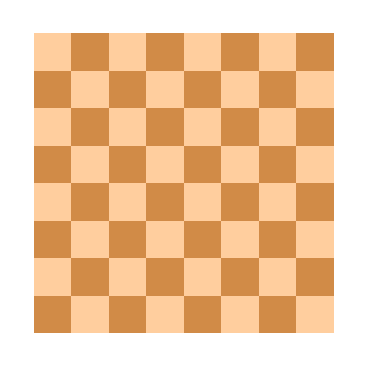

```mathematica
dark=RGBColor[0.8196,0.5451,0.2784];
light=RGBColor[1,0.8078,0.6196];

range=Partition[Range[64],8];
range=MapAt[Boole[EvenQ[#]]&,range,1;;8;;2];
range=MapAt[Boole[OddQ[#]]&,range,2;;8;;2];

board=Array[List,{8,8}];

drawBoard[board_]:=ArrayPlot[range,ColorRules->{0->light,1->dark},Epilog->(Inset[pieceObj["BlackQueen"]["Image"],#-1,#-1,1]&/@Position[board,1])]
(*ListAnimate[drawBoard/@{{{0,1,0,0,0,0,0,0}}}]*)
drawBoard[{{1,0,1,0,0,0,0,0}}]
```

```mathematica
stateNameArray=({{♜, ♞, ♝, ♛, ♚, ♝, ♞, ♜}, {♟, ♟, ♟, ♟, ♟, ♟, ♟, ♟}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □}, {♙, ♙, ♙, ♙, ♙, ♙, ♙, ♙}, {♖, ♘, ♗, ♕, ♔, ♗, ♘, ♖}});
```

```mathematica
coords=Table[file<>ToString[rank],{rank,Range[8]},{file,Alphabet[]⟦;;8⟧}];
coords//Reverse//MatrixForm
```

(a8 | b8 | c8 | d8 | e8 | f8 | g8 | h8
a7 | b7 | c7 | d7 | e7 | f7 | g7 | h7
a6 | b6 | c6 | d6 | e6 | f6 | g6 | h6
a5 | b5 | c5 | d5 | e5 | f5 | g5 | h5
a4 | b4 | c4 | d4 | e4 | f4 | g4 | h4
a3 | b3 | c3 | d3 | e3 | f3 | g3 | h3
a2 | b2 | c2 | d2 | e2 | f2 | g2 | h2
a1 | b1 | c1 | d1 | e1 | f1 | g1 | h1)

h

```mathematica
state=AssociationThread[Flatten[coords] -> Flatten[stateNameArray]];
state["a1"]
```

BlackRook

```mathematica
plotCoordAssoc=AssociationThread[Flatten[coords] -> Flatten[stateNameArray]];
```

```mathematica
ri = 1;
rf = 8;

whiteUp = 
	Table[
		{file, rank} -> Alphabet[]⟦file⟧ <> ToString[rank],
		{file, ri, rf, 1},
		{rank, ri, rf, 1}
		] //Flatten //Association;

whiteDown = 
	Table[
		{file, rank} -> Alphabet[]⟦1 + rf - file⟧ <> ToString[1 + rf - rank],
		{file, ri, rf, 1},
		{rank, ri, rf, 1}
		] //Flatten //Association;
		

whiteLeft = 
	Table[
		{rank, file} -> Alphabet[]⟦1 + rf - file⟧ <> ToString[1 + rf - rank],
		{file, ri, rf, 1},
		{rank, ri, rf, 1}
		] //Flatten //Association;
		
whiteRight = 
	Table[
		{rank, file} -> Alphabet[]⟦file⟧ <> ToString[rank],
		{file, ri, rf, 1},
		{rank, ri, rf, 1}
		] //Flatten //Association;
```

```mathematica
state⟦whiteUp[{1,1}]⟧
```

BlackRook

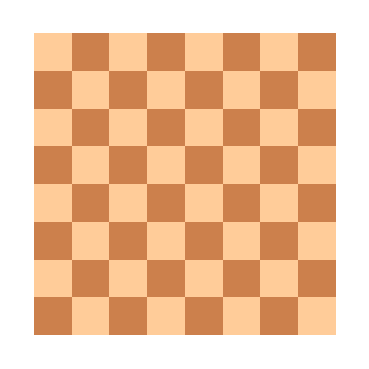

```mathematica
insetList = 
	Table[
		Inset[
			pieceObj[state⟦whiteDown[{i, j}]⟧]["Image"], 
			{i, j} - {1, 1}, 
			{i, j} - {1, 1}, 
			1
		],
		{i, 8}, 
		{j, 8}
	];

dark  = RGBColor[0.8, 0.5, 0.3];
light = RGBColor[1, 0.8, 0.6];

range=Partition[Range[64],8];
range=MapAt[Boole[EvenQ[#]]&,range,1;;8;;2];
range=MapAt[Boole[OddQ[#]]&,range,2;;8;;2];

ArrayPlot[
	range,
	ColorRules -> {0 -> light, 1 -> dark}, 
	Epilog -> insetList
]
```

```mathematica
vowels={"æ","eɪ","ɒ","ɔ","ɛ","i","ɝ","ɪ","aɪ","ɒ","oʊ","u","ʊ","ɔɪ","aʊ","ʌ","ə"};
With[{image=Import["https://upload.wikimedia.org/wikipedia/en/0/04/Vowel_triangle%2C_intermediate_vowels.png"]},pos=Transpose[{RandomReal[ImageDimensions[image][[1]],Length[vowels]],RandomReal[ImageDimensions[image][[2]],Length[vowels]]}];
LocatorPane[Dynamic[pos],image,Appearance->Function[Style[#,Red,20]]/@vowels]]
```